# ICARUS Spectrum Code

ICARUS - Inverse Compton Scattering Semi-Analytical Recoil -Corrected Ultra-Relativistic Spectrum Code
• Parallel processing code designed to run on apsv2 DL server
• Generates head-on point source spectra from Gaussian electron bunch and laser pulse distributions. Takes into account energy spread of electron bunch and laser pulse, emittance in 2D and polarisation.
• Based on the work of C. Sun [PRSTAB 14, 044701 (2011)], “Flew too close to C. Sun, Got burnt”. Parallel processing, feasible laser mode calculation and correction to spectral yield imposed.
• Benchmarked against ICCS3D by Balsa Terzic + Geoff Krafft, with strong agreement, almost identical.

Code History
An extension of the SUN1D (Eγ vs dNγ/dEγ ) to SUN2D. Previously in SUN1D (16) PRSTAB 12, 062801 (2009) the vertical emittance effect is neglected, as storage ring beams are used. ERL’s use circular beams so a 2D calculation is required, this is also needed to benchmark an improvement (relating to when source size and collimator size are similar) to ICCS3D by Balsa Terzic. The 2D model uses (3.18) of C. Sun’s thesis (also found in (A8) PRSTAB 14, 044701 (2011)). Code has subsequently been upgraded to ICARUS, utilizing high performance computing.

Potential Error Sources
• The integral over k goes from ∞ to 0 to sum over all modes (confirmed by Geoff) in the laser but its impractical. Implemented k ± 3Δk to just go for the fundamental harmonic + a bandwidth. Convergence tested succesfully.
• Terms such as N_laser and z_R which are outside the integration are actually dependent on λ and therefore k. I can understand N_Laser as it is taking the average and it is invariant but z_R seems more spurious. z_R is held constant throughout currently. (Geoff says taking these as constant is the best approximation we can do).
• Currently the code does not take the laser bandwidth variation into account with the cross section, whilst this is predicted to be a small effect it is still not a full treatment of laser energy spread. In practice this means that EL is kept constant during integration. Maybe this full treatment could be added though?

## Units, Constants and Simulation Setup

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
```

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Plot Units*)
phkeVnC=(keV*nC)/elecharge;
phMeVnC=(MeV*nC)/elecharge;
```

```mathematica
(*Simulation Setup*)
NKERNEL=35;
NQMC=20*10^6;
```

## Cases

```mathematica
(*Cases - CBETA 150MeV 0.5% BW*)
CBETA150={Ee->150MeV,Q->32pC,Epulse->62μJ,λ->1064nm,θcol->0.43333mrad,ϕ->0,ϵnx->0.3mm mrad,βx->0.126176,ϵny->0.3mm mrad,βy->0.126176,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"keV"};

DIANA340={Ee->340MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.18848mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.3592,ϵny->0.5mm mrad,βy->0.3592,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA680={Ee->680MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.09461mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.7181,ϵny->0.5mm mrad,βy->0.7181,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1020={Ee->1020MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol0->0.06328mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0756,ϵny->0.5mm mrad,βy->1.0756,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};

NEQSRNRF1={Ee->245.58MeV,Q->1nC,Epulse->100μJ,λ->532nm,θcol->0.239mrad,ϕ->0,ϵnx->1mm mrad,βx->0.3459,ϵny->1mm mrad,βy->0.3459,σL->25μm,ΔEe->8.6*10^-4,Δk->5*10^-4,L->10,npts->70,range->"MeV"};
NEQSRNRF2={Ee->245.58MeV,Q->1nC,Epulse->100μJ,λ->656nm,θcol->0.239mrad,ϕ->0,ϵnx->1mm mrad,βx->0.3459,ϵny->1mm mrad,βy->0.3459,σL->25μm,ΔEe->8.6*10^-4,Δk->5*10^-4,L->10,npts->70,range->"MeV"};

CLS300NdYAG={Ee->99.71MeV,Q->200pC,Epulse->100μJ,λ->1064nm,θcol->0.873mrad,ϕ->0,ϵnx->1mm mrad,βx->7.49cm,ϵny->1mm mrad,βy->7.49cm,σL->25μm,tpulse->5ps,ΔEe->8.6*10^-4,Δk->6.5*10^-4,L->10,npts->70,range->"keV"};
CLS300HoYAG={Ee->99.71MeV,Q->200pC,Epulse->100μJ,λ->2120nm,θcol->0.873mrad,ϕ->0,ϵnx->1mm mrad,βx->7.49cm,ϵny->1mm mrad,βy->7.49cm,σL->25μm,tpulse->5ps,ΔEe->8.6*10^-4,Δk->6.5*10^-4,L->10,npts->70,range->"keV"};

(*DIANA Latest Configurations: Subscript[E, inj] = 7 MeV, Subscript[E, Acc] = 15, 22.24 MV/m, Fundamental Harmonic*) 
DIANA347={Ee->347MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.18848mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.3592,ϵny->0.5mm mrad,βy->0.3592,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA687={Ee->687MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.09461mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.7181,ϵny->0.5mm mrad,βy->0.7181,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1027={Ee->1027MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.06328mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0756,ϵny->0.5mm mrad,βy->1.0756,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};

DIANA511={Ee->511MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.12567mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.5396473415644379,ϵny->0.5mm mrad,βy->0.5396473415644379,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1015={Ee->1015MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.06359mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0706237174466873,ϵny->0.5mm mrad,βy->1.0706237174466873,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1519={Ee->1519MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.04269mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.6003780693786585,ϵny->0.5mm mrad,βy->1.6003780693786585,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
```

npts determines the no. points used to produce the spectrum, range states whether you want a keV or MeV units system, Ee is the kinetic energy of the electron beam. Δk is the laser wavenumber spread (just laser energy spread as proportional).

```mathematica
trialcase=CBETA150;
```

## Polarisation

The polarisation term is negligible for the case where the polarisation is in the x-axis of the scattering plane (my answer) or we can notice the term vanishes at θ_f goes to zero, i.e. in the forward direction. This means you can just drop the term entirely and it won’t make much difference in the final result (Geoff’s answer). By this line of reasoning we can set τ, the azimuthal angle of the linear polarisation P_t with respect to the x_eaxis to zero and set ϕ_f, the azimuthal angle of the scattering plane to zero. τ = 0 , ϕ_f =0

```mathematica
(*τ=0;
ϕf=0;*)
τ=0;
ϕf=0;
```

## Scattered Photon Energy Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ;(*in eV, hbar is in eV, 2π due to hbar*)
```

EL is the energy of the incident photon in eV. EL is independent of k, this is currently used for the “averaged” values of N_L and z_R and also used in the “averaged” cross section terms.

## Scattered Photon Energy

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
Eγset[λ,Ee,ϕ,θcol]/.trialcase
```

396834.

## Sun Preliminaries

```mathematica
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/(β[Ee]*γ[Ee]);
ϵy[Ee_,ϵny_]:=ϵny/(β[Ee]*γ[Ee]);
zr[λ_,σL_]:=(4*π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee;
klaser[λ_]:=(2π)/λ;
σk[Δk_,λ_]:=Δk*klaser[λ];
```

The σ_k term usage here could be wrong. It is undefined in Sun’s works, it has been assumed to mirror the form used for the electron bunch energy spread.

## Collimation

```mathematica
R[L_,θcol_]:=L*θcol;(*Far field collimation, small angle approximation*)
```

```mathematica
(*Circular Collimation*)
x0[L_,θcol_]:=R[L,θcol];
y0[L_,θcol_,xd_]:=Re[Sqrt[R[L,θcol]^2-xd^2]];
(*Square Collimation*)
(*x0[A_]:=A;
y0[B_]:=B;*)
```

Square aperture created in two dimensions (x_0= A for x_d, y_0=B for x_d), Circular aperture based on the radius (x_0=R for x_d, y_0= Re Sqrt[R^2 - x_d^2] for y_d or vice versa depending on order of integration).

## Sun Intermediaries

Here we assume collisions are done at a waist i.e α_x=α_y= 0. Therefore, the ξ_(x/y) formula are simplified from Sun’s thesis.

```mathematica
γbar[λ_,Eγ_,θx_,θy_]:=(2*Eγ*EL[λ])/(me*(4*EL[λ]-Eγ*(θx^2+θy^2)))*(1+Sqrt[1+((4*EL[λ]-Eγ*(θx^2+θy^2))*me^2)/(4*EL[λ]^2*Eγ)]);
ξx[βx_,L_,k_,Ee_,ϵnx_,λ_,σL_]:=1+(βx/L)^2+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ξy[βy_,L_,k_,Ee_,ϵny_,λ_,σL_]:=1+(βy/L)^2+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
ζx[k_,βx_,Ee_,ϵnx_,λ_,σL_]:=1+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζy[k_,βy_,Ee_,ϵny_,λ_,σL_]:=1+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,k_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,k,Ee,ϵnx,λ,σL])/(βx*ζx[k,βx,Ee,ϵnx,λ,σL])];
σθy[Ee_,ϵny_,βy_,L_,k_,λ_,σL_]:=Sqrt[(ϵy[Ee,ϵny]*ξy[βy,L,k,Ee,ϵny,λ,σL])/(βy*ζy[k,βy,Ee,ϵny,λ,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θymax[λ_,Eγ_]:=Sqrt[(4*EL[λ])/Eγ];
θxmax[λ_,Eγ_,θy_]:=Sqrt[(4*EL[λ])/Eγ-θy^2];
```

The limits of integration have both been constructed using EL i.e the constant case. I’m unsure whether this is correct? Feels slightly incorrect, but simpler to get code running like this.

```mathematica
kmin[λ_,Δk_]:=klaser[λ]*(1-3*Δk);
kmax[λ_,Δk_]:=klaser[λ]*(1+3*Δk);
```

## Prefactor

```mathematica
prefactor[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_]:=(re^2*Ne[Q]*NL[Epulse,λ])/(4*π^3*hbar*clight*zr[λ,σL]*σγ[ΔEe,Ee]*σk[Δk,λ]*L^2);
```

```mathematica
prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]/.trialcase//ScientificForm
```

5.12004×10^-5

## Separated Integral Terms

```mathematica
term1[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_]:=1/(Sqrt[ζx[k,βx,Ee,ϵnx,λ,σL]*ζy[k,βy,Ee,ϵny,λ,σL]]*σθx[Ee,ϵnx,βx,L,k,λ,σL]*σθy[Ee,ϵny,βy,L,k,λ,σL]);
```

```mathematica
term2[λ_,Eγ_,θx_,θy_]:=γbar[λ,Eγ,θx,θy]/(1+(2*γbar[λ,Eγ,θx,θy]*EL[λ])/me);
```

```mathematica
term3[λ_,Eγ_,θx_,θy_,τ_,ϕf_]:=(1/4*((4*γbar[λ,Eγ,θx,θy]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))+(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))/(4*γbar[λ,Eγ,θx,θy]^2*EL[λ]))-2*Cos[τ-ϕf]^2*(γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))/((1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))^2));
```

```mathematica
term4[θx_,xd_,L_,Ee_,ϵnx_,βx_,k_,λ_,θy_,yd_,ϵny_,βy_,Eγ_,ΔEe_,Δk_,σL_]:=Exp[-(θx-xd/L)^2/(2*σθx[Ee,ϵnx,βx,L,k,λ,σL]^2)-(θy-yd/L)^2/(2*σθy[Ee,ϵny,βy,L,k,λ,σL]^2)-(γbar[λ,Eγ,θx,θy]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)-(k-klaser[λ])^2/(2*σk[Δk,λ]^2)];
```

## Integral Term

```mathematica
intterm[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,θx_,θy_,τ_,ϕf_,xd_,yd_,ΔEe_,Δk_]:=term1[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL]*term2[λ,Eγ,θx,θy]*term3[λ,Eγ,θx,θy,τ,ϕf]*term4[θx,xd,L,Ee,ϵnx,βx,k,λ,θy,yd,ϵny,βy,Eγ,ΔEe,Δk,σL]
```

```mathematica
INTterm[βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,τ_,ϕf_,ΔEe_,Δk_]:=NIntegrate[intterm[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,θx,θy,τ,ϕf,xd,yd,ΔEe,Δk]/.trialcase,{xd,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yd,-y0[L,θcol,xd]/.trialcase,y0[L,θcol,xd]/.trialcase},{θy,-θymax[λ,Eγ]/.trialcase,θymax[λ,Eγ]/.trialcase},{θx,-θxmax[λ,Eγ,θy]/.trialcase,θxmax[λ,Eγ,θy]/.trialcase},{k,kmin[λ,Δk]/.trialcase,kmax[λ,Δk]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->NQMC}];
```

## Spectral Density Calculation

```mathematica
dNdEγ[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_,βx_,ϵnx_,βy_,ϵny_,Eγ_,τ_,ϕf_]:=prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]*INTterm[βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,τ,ϕf,ΔEe,Δk];
```

```mathematica
LaunchKernels[NKERNEL];
```

```mathematica
Off[NIntegrate::maxp];
```

```mathematica
DistributeDefinitions[{dNdEγ,Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC],Which[(range/.trialcase)=="keV",keV,(range/.trialcase)=="MeV",MeV],Eγset,trialcase}];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::maxp]];
```

```mathematica
SpecDen=ParallelTable[{Eγ/Which[(range/.trialcase)=="keV",keV,(range/.trialcase)=="MeV",MeV],Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC]/((Q/.trialcase)/elecharge)*dNdEγ[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L,βx,ϵnx,βy,ϵny,Eγ,τ,ϕf]/.trialcase},{Eγ,Eγset[λ,Ee*(1-15*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,((Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]-Eγset[λ,Ee*(1-15*ΔEe),ϕ,θcol])/npts)/.trialcase}]//AbsoluteTiming;
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,947,34].

Kernels::rdead: Subkernel connected through KernelObject[25,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {11} assigned to KernelObject[25,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,943,30].

Kernels::rdead: Subkernel connected through KernelObject[21,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {15} assigned to KernelObject[21,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,942,29].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[20,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {16} assigned to KernelObject[20,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[25,local,<defunct>] resurrected as KernelObject[36,local].

LaunchKernels::clone: Kernel KernelObject[21,local,<defunct>] resurrected as KernelObject[37,local].

LaunchKernels::clone: Kernel KernelObject[20,local,<defunct>] resurrected as KernelObject[38,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 1.959 and 0.0574818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 2.23324 and 0.0649508 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 2.51921 and 0.0723048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 2.81835 and 0.0803517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 3.14257 and 0.0890917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 3.50609 and 0.0975515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 4.89345 and 0.127782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 11.4162 and 0.27908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 12.5037 and 0.301642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 13.5997 and 0.32297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 15.8798 and 0.358019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 18.4245 and 0.401351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 22.9456 and 0.473452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 26.4056 and 0.528408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 30.3663 and 0.599309 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 34.4846 and 0.654857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 36.4193 and 0.675873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 5.99124 and 0.151487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 6.61101 and 0.163056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 7.34526 and 0.17868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 14.7185 and 0.341037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 21.3487 and 0.448831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 1.48946 and 0.0440754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 3.91949 and 0.106141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 10.3266 and 0.256026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 4.38511 and 0.116201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 32.4533 and 0.630521 for the integral and error estimates.

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[84,local,<defunct>] failed.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 38.2873 and 0.697142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 1.70699 and 0.050202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 64.6452 and 0.976138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 61.9665 and 0.937437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 65.7724 and 0.980785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 60.8758 and 0.997128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 62.9092 and 0.952567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 63.8149 and 0.966226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 24.624 and 0.499058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 40.1329 and 0.718325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 41.9769 and 0.736293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 43.8361 and 0.751656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 60.9666 and 0.923084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 45.7378 and 0.771942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 59.8587 and 0.9102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 17.1085 and 0.378157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 19.8381 and 0.424946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 49.5936 and 0.829948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 51.3812 and 0.850416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 55.8825 and 0.87167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 57.2706 and 0.882195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 58.616 and 0.896518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 5.42927 and 0.139899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 8.23143 and 0.202138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 28.3233 and 0.563162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 52.9964 and 0.860838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 47.68 and 0.800689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 54.4727 and 0.865959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 9.24726 and 0.230066 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 66.0178 and 0.978251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 65.8904 and 0.996157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 0.0953973 and 0.00362659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 43.2165 and 0.848778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 9.55713 and 0.261442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 66.1439 and 0.9776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 30.5934 and 0.672991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 66.1851 and 0.98392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 64.519 and 1.00475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 65.3193 and 0.980858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 53.821 and 0.953933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 18.621 and 0.458427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 0.40998 and 0.0145399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 4.07719 and 0.122766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 20000000 integrand evaluations. NIntegrate obtained 1.43083 and 0.046966 for the integral and error estimates.

```mathematica
CloseKernels[];
```

```mathematica
SpecDen⟦1⟧/60
```

28.99

```mathematica
(*Get["GetNameFunction"]; 
SpeakName;*)
```

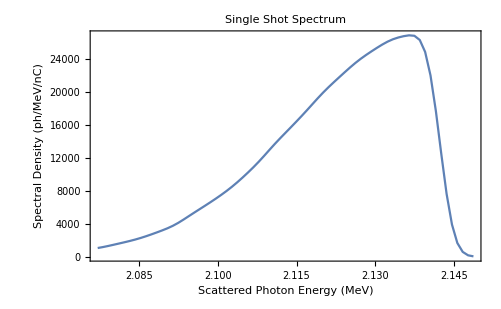

```mathematica
ListLinePlot[SpecDen⟦2⟧,Frame->True,PlotLabel->"Single Shot Spectrum",LabelStyle->15,FrameLabel->Which[(range/.trialcase)=="keV",{"Scattered Photon Energy (keV)","Spectral Density (ph/keV/nC)"},(range/.trialcase)=="MeV",{"Scattered Photon Energy (MeV)","Spectral Density (ph/MeV/nC)"}],PlotRange->Full]
```

## Spectral Density Per Electron

```mathematica
SpecDenElectron=Partition[Riffle[SpecDen⟦2⟧⟦All,1⟧,(SpecDen⟦2⟧⟦All,2⟧)/Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC]],2];
```

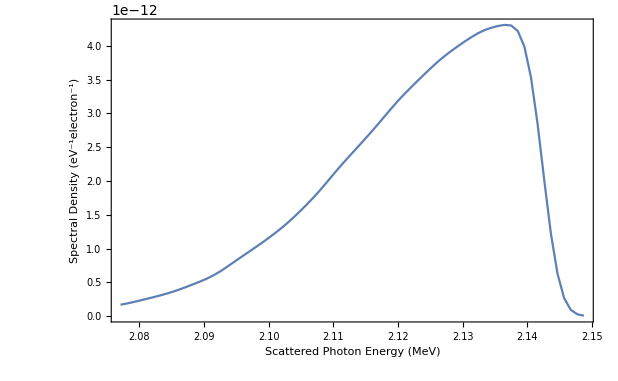

```mathematica
ListLinePlot[SpecDenElectron,Frame->True,FrameLabel->Which[(range/.trialcase)=="keV",{"Scattered Photon Energy (keV)","Spectral Density (eV^-1electron^-1)"},(range/.trialcase)=="MeV",{"Scattered Photon Energy (MeV)","Spectral Density (eV^-1electron^-1)"}],PlotRange->Full]
```

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA"];
SpecDen⟦2⟧>>"DIANA340_20M.txt";
SpecDenElectron>>"DIANA340_20Me-.txt";
```

# Benchmarking

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## ICCS3D Comparison

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA"];
CBETA150N200M=<<"CBETA150_200mil.txt";
```

```mathematica
rawdata=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA/CBETA150_ICCS3D_FINAL.txt","Words"];
ndata=Length[rawdata];
ncolumns=6;
ndat=ndata/ncolumns;
BalsaICCS=Array[Ω,{2,ndat}];
For[i=0,i<(ndat+1),i++,
(*for energy*)
Ω[1,i]=Interpreter["Number"][ToString[rawdata⟦1+ncolumns*(i-1)⟧]]*10^-3;
(*for specden*)
Ω[2,i]=Interpreter["Number"][ToString[rawdata⟦3+ncolumns*(i-1)⟧]]*phkeVnC;
];
BalsaVals=Array[Υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCS]]+1,i++,
If[BalsaICCS⟦2,i⟧>10^-30,
AppendTo[BalsaVals⟦1⟧,BalsaICCS⟦1,i⟧];
AppendTo[BalsaVals⟦2⟧,BalsaICCS⟦2,i⟧];
];
];
```

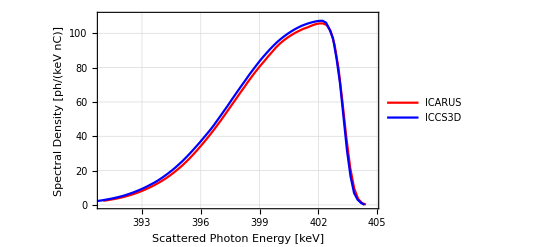

```mathematica
ListLinePlot[{CBETA150N200M,Transpose[BalsaVals]},Frame->True,LabelStyle->15,PlotStyle->{Red,Blue},FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},PlotRange->{{391,404.8},{0,110}},GridLines->True,PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->12,LegendFunction->frame],{0.25,0.75}]]
```

## Time vs Kernels

```mathematica
tvK10M={{1,3,5,7,9,10,12,15,20},{2165.80,895.06,747.85,682.30,675.13,668.61,680.16,706.59,733.39}/60};
```

```mathematica
tvK20M={{1,3,5,6,7,8,10,10,15,20,30},{4363.95,1843.88,1650.13,1416.11,1411.01,1441.09,1486.00,1487.30,1548.11,1753.55,1764.42}/60};
```

```mathematica
tvK100M={{7},{7726.40}/60};
```

```mathematica
tvK200M={{7},{71329.87}/60};
```

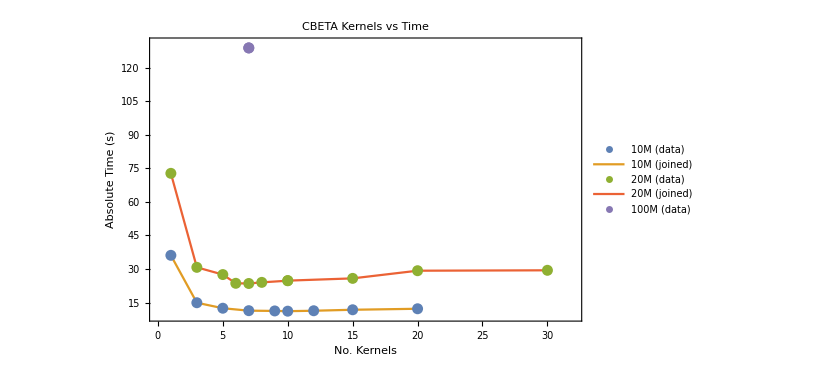

```mathematica
ListPlot[{Transpose[tvK10M],Transpose[tvK10M],Transpose[tvK20M],Transpose[tvK20M],Transpose[tvK100M]},Joined->{False,True,False,True,False},Frame->True,LabelStyle->15,FrameLabel->{"No. Kernels","Absolute Time (min)"},PlotLabel->"CBETA Kernels vs Time",PlotRange->{{0,32},{(Min[tvK10M⟦2⟧]-2),(Max[tvK100M⟦2⟧]+2)}},PlotLegends->Placed[LineLegend[{"10M (data)","10M (joined)","20M (data)","20M (joined)","100M (data)"},LabelStyle->12,LegendFunction->frame],{0.75,0.75}]]
```

```mathematica
tvperM7K={{10,20,30,50,70,100},{682.3/10,1411.01/20,2305.25/30,2427.76/50,6056.21/70,7726.4/100}};
```

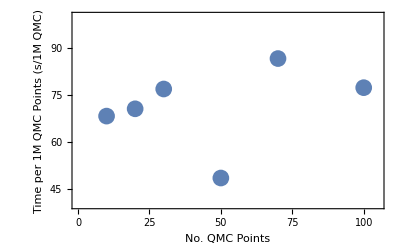

```mathematica
ListPlot[Transpose[tvperM7K],Frame->True,LabelStyle->15,FrameLabel->{"No. QMC Points","Time per 1M QMC Points (s/1M QMC)"},PlotRange->{{0,105},{40,100}},PlotStyle->PointSize[0.03]]
```

Actually for the anomalous 50M points, 50M was asked for and only ~31M delivered. Mathematicas weird thing where sometimes it ignores the value of QMC points you give it.